#### Value function for intrinsic policy, v_int ; Variance of OU process ψ(s); Value function of OU policy, vOU; Total value function, vFull(s_c)

```mathematica
vint[ϕst_,ko_, s_, sc_]:=ϕst/ko(Exp[-ko s/ϕst]-Exp[-ko sc/ϕst])
(*ψ[s_,sc_,vo_,d_,ν_]:=(vo^2 d)/ν^3((2 ν (s-sc))/vo - Exp[-2ν(s-sc)/vo]+4Exp[-ν(s-sc)/vo]-3)+0.01*)
ψ[s_,sc_,vo_,d_,ν_]:=(vo^2 d)/ν^3((2 ν (s-sc))/vo - Exp[-2ν(s-sc)/vo]+4Exp[-ν(s-sc)/vo]-3)
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]:= (σ/2 μ)/(2 ψ[s,sc,vo,d,ν])^(1/2)*)
vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]:= μ Erf[(σ/2)/( ψ[s,sc,vo,d,ν])^(1/2)]
vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] := vint[ϕst,ko, 0, sc]+vOU[sSt,sc,vo,d,ν, σ, μ]
```

Evolution of value function of intrinsic policy

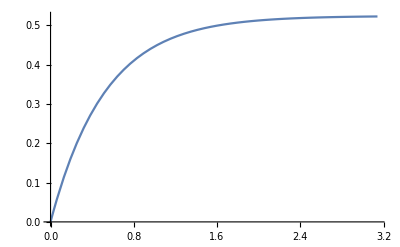

```mathematica
Plot[vint[π/6,1,0,sc],{sc,0,π},PlotRange->Automatic]
```

Evolution of variance of OU process

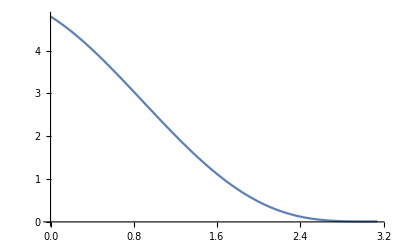

```mathematica
Plot[ψ[sc+2Cos[sc/2],sc,1,(π-sc),1],{sc,0,π},PlotRange->Automatic]
```

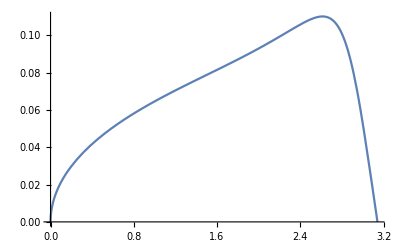

```mathematica
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]*)
Plot[vOU[π,sc,1,sc^-1,1, 0.1,( π-sc)],{sc,0,π},PlotRange->Automatic]
```

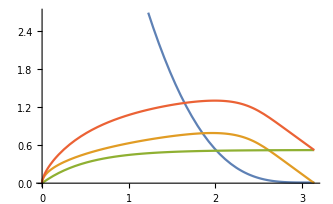

```mathematica
plt = Plot[{ψ[π,sc,1,π-sc,1],vOU[π,sc,1,sc^-1,1, 1, π-sc],vint[π/6,1,0,sc], vOU[π,sc,1,sc^-1,1, 1, π-sc]+vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
(*Export["plot.pdf",plt]*)
```

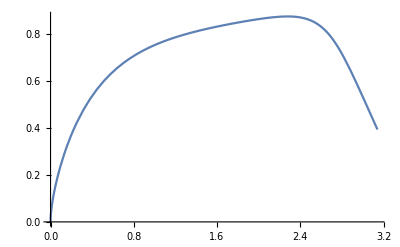

```mathematica
(*vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] *)
Plot[vFull[sc+2 Cos[sc/2], sc,1,sc^-1,1,0.5,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```

#### Non-dimensional functional forms

Considering success within a circle of radius σ

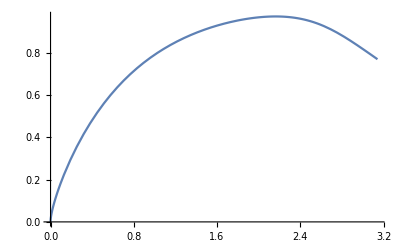

```mathematica
vintND[ϕst_,k_, s_, sc_]:=ϕst/k(Exp[-k s/ϕst]-Exp[-k sc/ϕst])
ψND[s_,sc_,pe_]:=pe(2  (s-sc) - Exp[-2(s-sc)]+4Exp[-(s-sc)]-3)+0.1
(*vOUND[s_,sc_,pe_, σ_, μ_]:= (σ/2 μ)/(2ψND[s,sc,pe])^(1/2)*)
vOUND[s_,sc_,pe_, σ_, μ_]:= μ Erf[(σ/2)/(2 ψND[s,sc,pe])^(1/2)]
vFullND[sSt_, sc_,pe_, σ_, μ_,ϕst_,k_] := vintND[ϕst,k, 0, sc]+vOUND[sSt,sc,pe, σ, μ]
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,0.3,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]
```

Considering success as intersecting a line of width σ/2

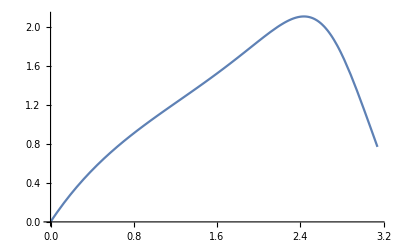

```mathematica
vintND[ϕst_,k_, s_, sc_]:=ϕst/k(Exp[-k s/ϕst]-Exp[-k sc/ϕst])
ψND[s_,sc_,pe_]:=pe(2  (s-sc) - Exp[-2(s-sc)]+4Exp[-(s-sc)]-3)+0.1
vOUND[s_,sc_,pe_, σ_, μ_]:= (σ μ)/ψND[s,sc,pe]
vFullND[sSt_, sc_,pe_, σ_, μ_,ϕst_,k_] := vintND[ϕst,k, 0, sc]+vOUND[sSt,sc,pe, σ, μ]
(*Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,(2 Cos[sc/2])/1,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]*)
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,0.3,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]
```

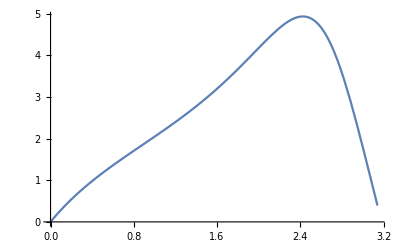

```mathematica
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,1,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```

#### Values used for curves in the paper

0.5

0.1

8.

0.3

π/8

0.0125

0.0625

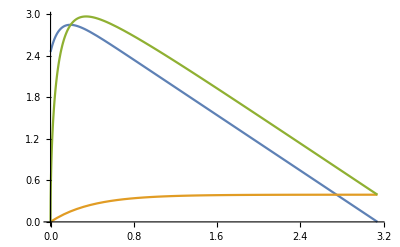

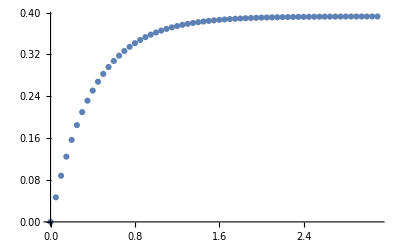

vInt_Pe_0.0125_lNu_0.0625.csv

Power::infy: Infinite expression 1/0. encountered.

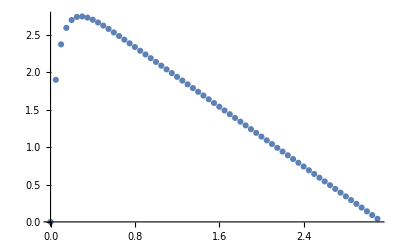

vOU_Pe_0.0125_lNu_0.0625.csv

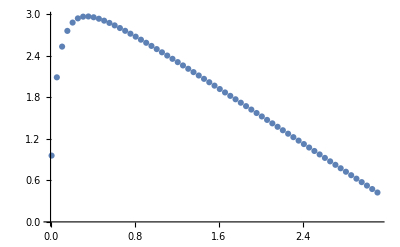

vFull_Pe_0.0125_lNu_0.0625.csv

```mathematica
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]
vint[ϕst_,ko_, s_, sc_]
vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_]*)
voF = 0.5
dF = 0.10
(*First Data*)
(*νF = 0.5*)
(*Second Data*)
(*νF = 1.0*)
(*Third Data*)
(*νF = 2.0*)
(*Fourth Data*)
(*νF = 4.0*)
(*Fifth Data*)
νF = 8.0
σF = 0.3
ϕstF = π/8
peF = dF/νF
lνF = voF/νF
Plot[{vOU[sc+2 Cos[sc/2],sc,voF,dF (sc+0.1)^-1,νF, σF, π-sc],vint[ϕstF,1,0,sc], vOU[sc+2 Cos[sc/2],sc,voF,dF sc^-1,νF, σF, π-sc]+vint[ϕstF,1,0,sc]},{sc,0,π},PlotRange->All]

tabLst = Table[{sc,vint[ϕstF,1,0,sc]},{sc,0,π,0.05}];
ListPlot[tabLst,PlotRange->All]
Export["vInt_Pe_"<>ToString[peF]<>"_lNu_"<>ToString[lνF]<>".csv",tabLst]

tabLst = Table[{sc,vOU[sc+2 Cos[sc/2],sc,voF,dF sc^-1,νF, σF, π-sc]},{sc,0,π,0.05}];
ListPlot[tabLst,PlotRange->All]
Export["vOU_Pe_"<>ToString[peF]<>"_lNu_"<>ToString[lνF]<>".csv",tabLst]

tabLst = Table[{sc,vOU[sc+2 Cos[sc/2],sc,voF,dF sc^-1,νF, σF, π-sc]+vint[ϕstF,1,0,sc]},{sc,0.01,π,0.05}];
ListPlot[tabLst,PlotRange->All]
Export["vFull_Pe_"<>ToString[peF]<>"_lNu_"<>ToString[lνF]<>".csv",tabLst]
```